```mathematica
a:=Plot[PrimePi[x],{x,0,1000},AxesLabel->{"Search Size",Automatic},PlotLabel->"Number of Primes Less Than Search Size"]
```

```mathematica
b:=Plot[PrimePi[x]/x,{x,0,1000},AxesLabel->{"Search Size",Automatic},PlotLabel->"Prime Density"]
```

```mathematica
c:=Plot[{PrimePi[x]/x,1/Log[x]},{x,0,1000},Filling->Axis,AxesLabel->{"Search Size",Automatic},PlotLabel->"Prime Density & Logarithmic Integral"]
```

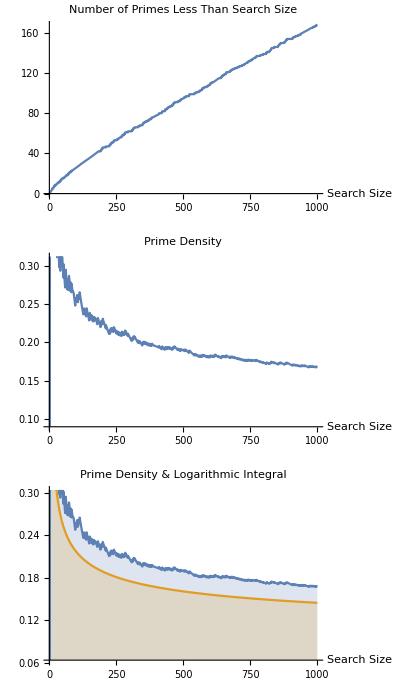

```mathematica
GraphicsColumn[{a,b,c},AspectRatio->Automatic]
```

```mathematica
CountPrime=Asymptotic[PrimePi[x],x->Infinity]
```

x/Log[x]

```mathematica
LogarithmicIntegral=Asymptotic[x/Log[x],x->Infinity]
```

x/Log[x]

```mathematica
ClearAll["Global'*"]
```